# Remi & Whitlock MEC

## Background selection

According to Hudson & Kaplan (1995, eq. 8), the effect of background selection (BGS) is apprximately

```mathematica
BHK95[U_,s_,h_,R_]:=Exp[-U/(2 s h+R)]
BHK95alt[u_,s_,r_,n_]:=Exp[-n (u s)/(2(s+r)^2)]
BRW18[u_,s_,r_]:=Exp[-Sum[(u⟦i⟧s⟦i⟧)/(s⟦i⟧+r⟦i⟧(1-s⟦i⟧))^2,{i,1,Length[u]}]]
BRW18alt[u_,s_,r_,n_]:=Exp[-n (u s)/(s+r(1-s))^2]
FstFunc[M_,B_]:=1/(1+2M B)
```

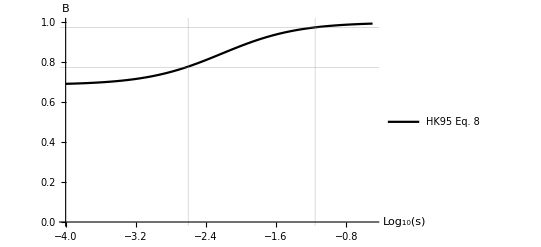

```mathematica
l=10 10^6; (* size of region in bp *)
pe=0.015; (* proportion of region that is exonic *)
μ=2.5 10^-8; (* deleterious mutation rate per bp *)
r=0.01; (* total map length of region in morgans *)
pl1=Plot[
BHK95[pe l μ,10^sExp,1,r],{sExp,-4,-0.5},
PlotRange->{Full,{0,1}},
AxesLabel->{"Log_10(s)",B},
GridLines->{{Log[10,0.0025],Log[10,0.07]},{(0.740+0.81)/2,0.975}},
PlotStyle->Black
(*PlotLabel->"HK95 Eq. 8"*),
PlotLegends->{"HK95 Eq. 8"}
]
```

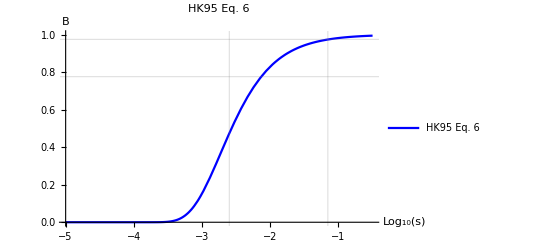

```mathematica
myu=2.5 10^-8;
myr=r/l;
myn=pe l;
pl2=Plot[
BHK95alt[myu,10^sExp,myr,myn],{sExp,-5,-0.5},
PlotRange->{Full,{0,1}},
AxesLabel->{"Log_10(s)",B},
GridLines->{{Log[10,0.0025],Log[10,0.07]},{(0.740+0.81)/2,0.975}},
PlotLabel->"HK95 Eq. 6",
PlotStyle->Blue,
PlotLegends->{"HK95 Eq. 6"}
]
```

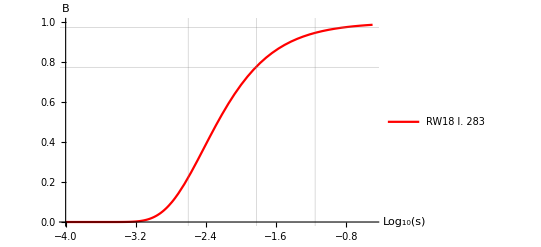

```mathematica
myu=2.5 10^-8;
myr=r/l;
myn=pe l;
pl3=Plot[
BRW18alt[myu,10^sExp,myr,myn],{sExp,-4,-0.5},
PlotRange->{Full,{0,1}},
AxesLabel->{"Log_10(s)",B},
GridLines->{{Log[10,0.0025],Log[10,0.07],Log[10,0.015]},{(0.740+0.81)/2,0.975}},
(*PlotLabel->"RW18 l. 283",*)
PlotStyle->Red,
PlotLegends->{"RW18 l. 283"}
]
```

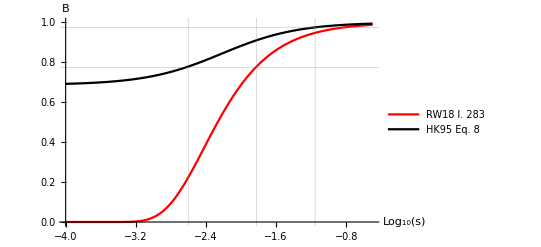

```mathematica
Show[pl3,pl1]
```

```mathematica
10^-1.8
```

0.0158489

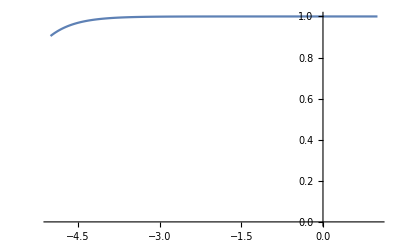

```mathematica
myu=1 10^-8;
myr=0.0001 10^-8;
myL=10^2;
Plot[BRW18[Table[myu,{myL}],Table[10^sExp,{myL}],Table[myr,{myL}]],{sExp,-5,1},PlotRange->{Full,{0,1}}]
```

```mathematica
Table[1,{10}]
```

{1,1,1,1,1,1,1,1,1,1}

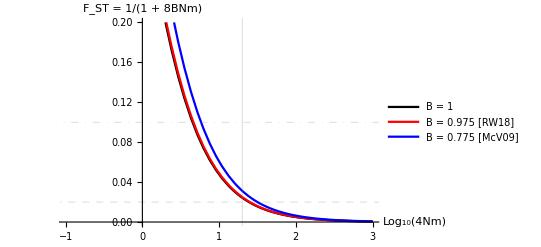

```mathematica
B1=0.975;
B2=(0.74+0.81)/2;
Plot[
{
FstFunc[10^MExp,1],
FstFunc[10^MExp,B1],
FstFunc[10^MExp,B2]
},{MExp,-1,3},
PlotStyle->{Black,Red,Blue},
PlotRange->{Full,{0,0.2}},
PlotLegends->{"B = 1","B = 0.975 [RW18]","B = 0.775 [McV09]"},
AxesLabel->{"Log_10(4Nm)","F_ST = 1/(1 + 8BNm)"},
GridLines->{{(*Log[10,4 0.05 1000],*)Log[10,4 0.005 1000](*,Log[10,4 0.05 10000]*)},{{0.02,Dashed},{0.1,DotDashed}}}
]
```

```mathematica
10^(.75)/(4*1000)
```

0.00140585

Plotting d_xy as a function of time for the complete-isolation (NM) model and the isolation-with-migration (IM) model at equilibrium.

```mathematica
Manipulate[
Plot[
{2 μ(2 Ne+t),
2μ(2Ne+1/(2 m)) 
},{t,0,16Ne},
PlotRange->{Full,{0,0.001}},
AxesLabel->{"t","d_xy"},
PlotLegends->{"NM model","IM model"}
],
{{Ne,10^3},10^1,10^4},{{m,10^-4},10^-5,10^-2}
]
```

Plotting the proportion of d_xy explained by 4 N μ.

```mathematica
Manipulate[
Plot[
{4μ Ne/(2 μ(2 Ne+t)),
4μ Ne/(2μ(2Ne+1/(2 m)) )
},{t,0,16Ne},
PlotRange->{Full,{0,1}},
AxesLabel->{"t","4μN_e/d_xy"},
PlotLegends->{"NM model","IM model"}
],
{{Ne,10^3},10^1,10^4},{{m,10^-4},10^-5,10^-2}
]
```

Under the NM and the IM models, F_ST converges to 1 and 1/(1+8 N_e m), respectively. Therefore, without migration, there will be a point in time where BGS will no longer affect F_ST, but with sufficient migration, BGS can affect F_ST independently of time.

```mathematica
TtIM=1/2 2 Ne +1/2(2Ne+1/(2m))
```

Ne+1/2 (1/(2 m)+2 Ne)

```mathematica
TtIM//Simplify
```

1/(4 m)+2 Ne

```mathematica
TsIM=2Ne
```

2 Ne

```mathematica
TtNM=1/2 2Ne+1/2(2Ne+t)
```

Ne+1/2 (2 Ne+t)

```mathematica
TsNM=2Ne
```

2 Ne

```mathematica
FstIM=(TtIM-TsIM)/TtIM//Simplify
```

1/(1+8 m Ne)

```mathematica
FstNM=(TtNM-TsNM)/TtNM//Simplify
```

t/(4 Ne+t)

```mathematica
Limit[FstNM,t->∞]
```

1

Plotting F_ST as a function of time (IM model: equilibrium only).

```mathematica
Manipulate[
Plot[
{t/(4 Ne+t),
1/(1+8Ne m) 
},{t,0,64Ne},
PlotRange->{Full,{0,1}},
AxesLabel->{"t","F_ST"},
PlotLegends->{"NM model","IM model"}
],
{{Ne,10^3},10^1,10^4},{{m,10^-4},10^-5,10^-2}
]
```

Derivative of d_xy and F_ST w.r.t. to N_e:

```mathematica
DerDxyNM=D[2u(2 Ne+t),Ne]//Simplify
```

4 u

```mathematica
DerDxyIM=D[2u(2 Ne+1/(2m)),Ne]//Simplify
```

4 u

```mathematica
DerFstNM=D[t/(4 Ne+t),Ne]//Simplify
```

-(4 t)/(4 Ne+t)^2

```mathematica
Limit[DerFstNM,t->∞]
```

0

```mathematica
DerFstIM=D[1/(1+8Ne m),Ne]//Simplify
```

-(8 m)/(1+8 m Ne)^2

```mathematica
Manipulate[
Plot[
{Abs[-(4 t)/(4 Ne+t)^2],
Abs[-(8 m)/(1+8 m Ne)^2]
},{t,0,100Ne},
PlotRange->{Full,Automatic},
AxesLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","SubscriptBox[StyleBox[\"F\",FontSlant->\"Italic\"], \"ST\"]"},
PlotLegends->{"NM model","IM model"}
],
{{Ne,10^3},10^1,10^4},{{m,10^-4},10^-5,10^-2}
]
```

```mathematica
Manipulate[
Plot[
{4 μ,
4μ
},{t,0,100Ne},
PlotRange->{Full,Automatic},
AxesLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","SubscriptBox[StyleBox[\"F\",FontSlant->\"Italic\"], \"ST\"]"},
PlotLegends->{"NM model","IM model"}
],
{{Ne,10^3},10^1,10^4},{{m,10^-4},10^-5,10^-2}
]
```

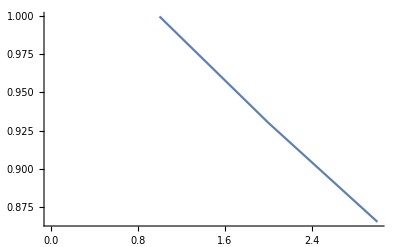

```mathematica
ListPlot[{1,1-s,(1-s)^2}/.{s->0.07},
Joined->True]
```